```mathematica
Clear["Global`*"]
```

```mathematica
fk[a_,b_,rd_,rmax_,u_]:=((a (b (-3 E^((2 (1+a+b))/rd)+3 E^((2 (2 a+b))/rd)-E^((2 (a+2 b))/rd)+E^((2+4 b)/rd)+E^((2 (1+a+rmax))/rd)-E^((2 (2 a+rmax))/rd)-3 E^((2 (1+b+rmax))/rd)+3 E^((2 (a+b+rmax))/rd)-3 E^((2 (1+a+b+rd u))/rd)-E^((2 (2 a+b+rd u))/rd)+3 E^((2 (a+2 b+rd u))/rd)-10 E^((2+2 a+2 b+rd u)/rd)-2 E^((4 a+2 b+rd u)/rd)-2 E^((2+4 b+rd u)/rd)-2 E^((2 a+4 b+rd u)/rd)-3 E^((2 (1+a+rmax+rd u))/rd)-E^((2 (2 a+rmax+rd u))/rd)+E^((2 (1+b+rmax+rd u))/rd)+3 E^((2 (a+b+rmax+rd u))/rd)+2 E^((2+2 a+2 rmax+rd u)/rd)+2 E^((4 a+2 rmax+rd u)/rd)+2 E^((2+2 b+2 rmax+rd u)/rd)+10 E^((2 a+2 b+2 rmax+rd u)/rd)+E^((2+4 b+2 rd u)/rd))-(E^((2 b)/rd)-E^((2 rmax)/rd)) (-1+E^u) (E^((4 a)/rd)-E^((2 (1+a))/rd)-E^((2 (1+b))/rd)+E^((2 (a+b))/rd)-E^((4 a)/rd+u)-3 E^((2+2 a+rd u)/rd)+E^((2+2 b+rd u)/rd)+3 E^((2 a+2 b+rd u)/rd)) rd)+(-E^(2/rd)+E^((2 a)/rd)) (-1+E^u) (-2 b^2 E^((a+b)/rd) (E^((2 b)/rd)+E^((2 rmax)/rd)) (-1+E^u)+b (E^((4 b)/rd)+3 E^((2 (a+b))/rd)-2 E^((a+3 b)/rd)-E^((2 (a+rmax))/rd)-3 E^((2 (b+rmax))/rd)+2 E^((a+b+2 rmax)/rd)-E^((4 b)/rd+u)+E^((2 a+2 b+rd u)/rd)+2 E^((a+3 b+rd u)/rd)+E^((2 a+2 rmax+rd u)/rd)-2 E^((a+b+2 rmax+rd u)/rd)-E^((2 b+2 rmax+rd u)/rd)) rd+(-E^(((2 a)/rd))+E^((2 b)/rd)) (E^((2 b)/rd)-E^((2 rmax)/rd)) (-1+E^u) rd^2)) rmax)/(2 a^2 E^((a+b)/rd) (E^(2/rd)+E^((2 a)/rd)) (E^((2 b)/rd)-E^((2 rmax)/rd)) (-1+E^u)^2 rmax+a (b (E^((2 (a+2 b))/rd) (1-3 rmax)+E^((2 (2 a+b+rd u))/rd) (1-3 rmax)+3 E^((2 (1+a+b))/rd) (1-rmax)+E^((2 (2 a+rmax))/rd) (1-rmax)+3 E^((2 (1+a+b+rd u))/rd) (1-rmax)+10 E^((2+2 a+2 b+rd u)/rd) (1-rmax)+2 E^((2+4 b+rd u)/rd) (1-rmax)+E^((2 (2 a+rmax+rd u))/rd) (1-rmax)+E^((2 (2 a+b))/rd) (-3+rmax)-E^((2 (1+b+rmax))/rd) (-3+rmax)+E^((2 (a+2 b+rd u))/rd) (-3+rmax)-E^((2 (1+a+rmax+rd u))/rd) (-3+rmax)+E^((2+4 b)/rd) (-1+rmax)+3 E^((2 (a+b+rmax))/rd) (-1+rmax)+3 E^((2 (a+b+rmax+rd u))/rd) (-1+rmax)+2 E^((4 a+2 rmax+rd u)/rd) (-1+rmax)+10 E^((2 a+2 b+2 rmax+rd u)/rd) (-1+rmax)+E^((2+4 b+2 rd u)/rd) (-1+rmax)+2 E^((4 a+2 b+rd u)/rd) (1+rmax)+2 E^((2 a+4 b+rd u)/rd) (1+rmax)-2 E^((2+2 a+2 rmax+rd u)/rd) (1+rmax)-2 E^((2+2 b+2 rmax+rd u)/rd) (1+rmax)+E^((2 (1+a+rmax))/rd) (-1+3 rmax)+E^((2 (1+b+rmax+rd u))/rd) (-1+3 rmax))-(-1+E^u) (E^((2+2 a+2 b+rd u)/rd) (-rd (-3+rmax)-6 rmax)+E^((2 (1+b+rmax))/rd) (rd (-1+rmax)-2 rmax)+E^((2+4 b)/rd) rd (1-rmax)+E^((2 a+4 b+rd u)/rd) rd (-3+rmax)+E^((2+2 a+2 rmax+rd u)/rd) rd (-3+rmax)-E^((2 (2 a+rmax))/rd) rd (-1+rmax)+E^((2+4 b+rd u)/rd) rd (-1+rmax)+E^((4 a+2 rmax+rd u)/rd) rd (-1+rmax)+2 E^((2+a+3 b)/rd) (-1+rd) rmax-2 E^((2+a+b+2 rmax)/rd) (-1+rd) rmax-2 E^((2+a+3 b+rd u)/rd) (-1+rd) rmax+2 E^((2+a+b+2 rmax+rd u)/rd) (-1+rd) rmax-2 E^((3 (a+b))/rd) (1+rd) rmax+2 E^((3 a+b+2 rmax)/rd) (1+rd) rmax+2 E^((3 a+3 b+rd u)/rd) (1+rd) rmax-2 E^((3 a+b+2 rmax+rd u)/rd) (1+rd) rmax+E^((2 (2 a+b))/rd) (rd (-1+rmax)+2 rmax)+E^((2 (a+2 b))/rd) rd (-1+3 rmax)+E^((2 (1+a+rmax))/rd) rd (-1+3 rmax)+E^((2 a+2 b+2 rmax+rd u)/rd) (-rd (-3+rmax)+6 rmax)+E^((2 (1+a+b))/rd) (rd-2 rmax-3 rd rmax)+E^((2 (a+b+rmax))/rd) (rd+2 rmax-3 rd rmax)+E^((4 a+2 b+rd u)/rd) (rd-2 rmax-rd rmax)+E^((2+2 b+2 rmax+rd u)/rd) (rd+2 rmax-rd rmax)))+(-1+E^u) (2 b^2 E^((a+b)/rd) (-E^(2/rd)+E^((2 a)/rd)) (E^((2 b)/rd)+E^((2 rmax)/rd)) (-1+E^u)+b (E^((2 (1+a+b))/rd) (-rd (-3+rmax)-2 rmax)+E^((2 (a+2 b))/rd) (rd (-1+rmax)-2 rmax)+E^((2+4 b)/rd) rd (1-rmax)+2 E^((2+a+b+2 rmax)/rd) (rd-rmax)-2 E^((3 a+b+2 rmax)/rd) (rd-rmax)-2 E^((2+a+b+2 rmax+rd u)/rd) (rd-rmax)+2 E^((3 a+b+2 rmax+rd u)/rd) (rd-rmax)+E^((2 (2 a+b))/rd) rd (-3+rmax)+E^((2 (1+b+rmax))/rd) rd (-3+rmax)-E^((2 (2 a+rmax))/rd) rd (-1+rmax)+E^((2+4 b+rd u)/rd) rd (-1+rmax)+E^((4 a+2 rmax+rd u)/rd) rd (-1+rmax)+2 E^((3 (a+b))/rd) (rd+rmax)-2 E^((2+a+3 b)/rd) (rd+rmax)+2 E^((2+a+3 b+rd u)/rd) (rd+rmax)-2 E^((3 a+3 b+rd u)/rd) (rd+rmax)+E^((2 (a+b+rmax))/rd) (-rd (-3+rmax)+2 rmax)+E^((2 (1+a+rmax))/rd) (rd (-1+rmax)+2 rmax)+E^((4 a+2 b+rd u)/rd) rd (-1+3 rmax)+E^((2+2 b+2 rmax+rd u)/rd) rd (-1+3 rmax)+E^((2+2 a+2 b+rd u)/rd) (rd-6 rmax-3 rd rmax)+E^((2 a+2 b+2 rmax+rd u)/rd) (rd+6 rmax-3 rd rmax)+E^((2+2 a+2 rmax+rd u)/rd) (rd-2 rmax-rd rmax)+E^((2 a+4 b+rd u)/rd) (rd+2 rmax-rd rmax))+(-E^(a/rd)+E^(b/rd)) (-1+E^u) rd (E^((2 a+3 b)/rd) (rd (-1+rmax)-2 rmax)+E^((2+b+2 rmax)/rd) (rd (-1+rmax)-2 rmax)+E^((2+3 b)/rd) rd (1-rmax)-E^((3 a+2 rmax)/rd) rd (-1+rmax)+E^((3 a+2 b)/rd) (rd (-1+rmax)+2 rmax)+E^((2+a+2 rmax)/rd) (rd (-1+rmax)+2 rmax)+E^((2+a+2 b)/rd) (rd-4 rmax-rd rmax)+E^((2 a+b+2 rmax)/rd) (rd+4 rmax-rd rmax))))
```

```mathematica
nmin=4;
nmax=6;
rdmin=-3;
rdmax=3;
datapoints=4;
d=1;
U01=-3;
U02=0;
a=8.5;
b=2.5;
at=a-b;
bt=a+b;
npoints=nmax-nmin;
Rsink=1;
Rmax=25;
t0=0;
t1=5000;
u1[r_]:=U01 Exp[-((r-a)/b)^n];
u2[r_]:=U02 Exp[-((r-a)/b)^n];
pde={D[ρ1[r,t],t]==2/r ρ1[r,t] u1'[r]+D[ρ1[r,t],r] u1'[r]+ρ1[r,t] u1''[r]+d 2/r D[ρ1[r,t],r]+d D[ρ1[r,t],r,r]-w12 ρ1[r,t]+w21 ρ2[r,t],D[ρ2[r,t],t]==2/r ρ2[r,t] u2'[r]+D[ρ2[r,t],r] u2'[r]+ρ2[r,t] u2''[r]+d 2/r D[ρ2[r,t],r]+d D[ρ2[r,t],r,r]-w21 ρ2[r,t]+w12 ρ1[r,t]};
bc={ρ1[Rsink,t]==0,ρ2[Rsink,t]==0,ρ1[Rmax,t]==w21/(w12+w21),ρ2[Rmax,t]==w12/(w12+w21)};
ic={ρ1[r,t0]==w21/(w12+w21)*(1-1/r),ρ2[r,t0]==w12/(w12+w21)*(1-1/r)};
ReactionRate=Table[0,{k,1,2},{i,1,datapoints+1},{j,1,npoints+1}];
```

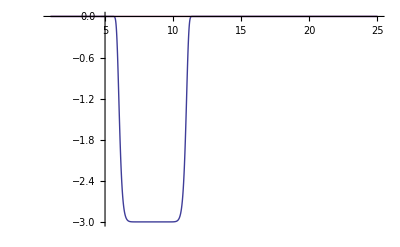

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

Donen=16i=0w12=500000.

{1.10949}

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

Donen=16i=1w12=500.

{1.11116}

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

General::stop: Further output of NDSolve :: ibcinc will be suppressed during this calculation.

Donen=16i=2w12=0.5

{1.26421}

Donen=16i=3w12=0.0005

{1.11022}

Donen=16i=4w12=5.×10^-7

{1.08501}

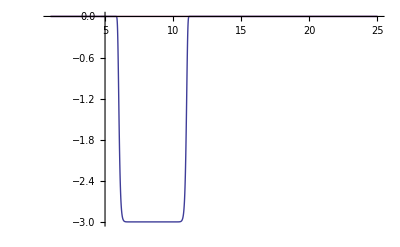

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

Donen=32i=0w12=500000.

{1.10952}

Donen=32i=1w12=500.

{1.11214}

Donen=32i=2w12=0.5

{1.24886}

Donen=32i=3w12=0.0005

{1.1102}

Donen=32i=4w12=5.×10^-7

{1.08443}

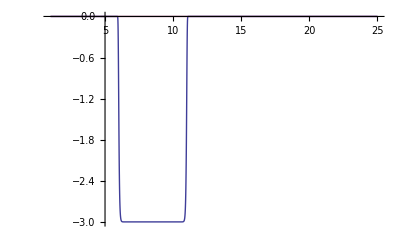

Donen=64i=0w12=500000.

{1.10959}

Donen=64i=1w12=500.

{1.11252}

Donen=64i=2w12=0.5

{1.23888}

Donen=64i=3w12=0.0005

{1.11021}

Donen=64i=4w12=5.×10^-7

{1.08416}

```mathematica
For[j=0,j≤npoints,j++,
n=2^(nmin+j);
Print[Plot[{u1[r],u2[r]},{r,Rsink,Rmax},PlotRange->All]];
For[i=0,i≤datapoints,i++,
rd=10^(rdmin+i*(rdmax-rdmin)/datapoints);
w21=d/(2*rd^2);
w12=w21;
sol=NDSolve[{pde,bc,ic},{ρ1,ρ2},{t,t1,t1},{r,Rsink,Rmax},MaxSteps->Infinity,MaxStepFraction->0.002,AccuracyGoal->15,StartingStepSize->0.001,WorkingPrecision->MachinePrecision,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->24000}}];
Print["Done","n=",n,"i=",i,"w12=",N[w12]];
ρ1eq[r_]=ρ1[r,t1]/.sol;
ρ2eq[r_]=ρ2[r,t1]/.sol;
ρtot[r_]=(ρ1[r,t1]+ρ2[r,t1])/.sol;
ReactionRate[[1,i+1,j+1]]=rd;
ReactionRate[[2,i+1,j+1]]=D[ρtot[r],r]/.r->1;
Print[N[D[ρtot[r],r]/.r->1]];
]]
```

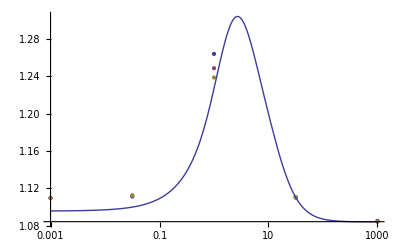

```mathematica
c1=Transpose[{ReactionRate[[1,All,1]],Flatten[ReactionRate[[2,All,1]]]}];
c2=Transpose[{ReactionRate[[1,All,1]],Flatten[ReactionRate[[2,All,2]]]}];
c3=Transpose[{ReactionRate[[1,All,1]],Flatten[ReactionRate[[2,All,3]]]}];
p1=ListLogLinearPlot[{c1,c2,c3}];
p2=LogLinearPlot[fk[at,bt,rd,Rmax,U01],{rd,(10^rdmin),(10^rdmax)}];
Show[p1,p2,PlotRange->All]
```

```mathematica
b=Table[0,{i,1,npoints+1}];
b[[1]]=N[ReactionRate[[1,All,1]]];
For[j=1,j≤npoints,j++,
b[[j+1]]=N[Flatten[ReactionRate[[2,All,j]]]];]
Export["numeric_rates.csv",Transpose[b]]

resolution=100;
c=Table[{N[10^rd],fk[at,bt,10^rd,Rmax,U01]},{rd,rdmin,rdmax,(rdmax-rdmin)/resolution}];
Export["analytic_rates.csv",N[c]]
```

numeric_rates.csv

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -ⅇ^50000.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating ⅇ^50000.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -ⅇ^50000.

General::stop: Further output of N :: meprec will be suppressed during this calculation.

analytic_rates.csv

```mathematica
n=2^4;
U01=-3
at=6;
bt=11;
Klim = (NIntegrate[Exp[u1[x]]/x^2,{x,Rsink,Rmax}])^(-1)
```

-3

SystemException[MemoryAllocationFailure,{Klim=1/NIntegrate[Exp[u1[x]]/x^2,{x,Rsink,Rmax}],1/NIntegrate[Exp[u1[x]]/x^2,{x,Rsink,Rmax}],NIntegrate[Exp[u1[x]]/x^2,{x,Rsink,Rmax}],{(NIntegrate[#1,Sequence[{x,Rsink,Rmax}]]&)[{(ⅇ^(-3 ⅇ^(-1.×10^48 (-8.5+x)^16)))/x^2,(ⅇ^(-3 ⅇ^(-1.×10^24 (-8.5+x)^16)))/x^2,(ⅇ^(-3 ⅇ^(-1. (-8.5+x)^16)))/x^2,(ⅇ^(-3 ⅇ^(-1.×10^-24 (-8.5+x)^16)))/x^2,(ⅇ^(-3 ⅇ^(-1.×10^-48 (-8.5+x)^16)))/x^2}],(NIntegrate[#1,Sequence[{x,Rsink,Rmax}]]&)[{(ⅇ^(-3 ⅇ^(-0.189681 (-8.5+x)^16)))/x^2,(ⅇ^(-3 ⅇ^(-0.185161 (-8.5+x)^16)))/x^2,(ⅇ^(-3 ⅇ^(-0.0234916 (-8.5+x)^16)))/x^2,(ⅇ^(-3 ⅇ^(-0.187708 (-8.5+x)^16)))/x^2,(ⅇ^(-3 ⅇ^(-0.271065 (-8.5+x)^16)))/x^2}],(NIntegrate[#1,Sequence[{x,Rsink,Rmax}]]&)[{(ⅇ^(-3 ⅇ^(-0.189588 (-8.5+x)^16)))/x^2,(ⅇ^(-3 ⅇ^(-0.182574 (-8.5+x)^16)))/x^2,(ⅇ^(-3 ⅇ^(-0.0285621 (-8.5+x)^16)))/x^2,(ⅇ^(-3 ⅇ^(-0.187755 (-8.5+x)^16)))/x^2,(ⅇ^(-3 ⅇ^(-0.273401 (-8.5+x)^16)))/x^2}]},{NIntegrate[(ⅇ^(-3 ⅇ^(-1.×10^48 (-8.5+x)^16)))/x^2,{x,Rsink,Rmax}],NIntegrate[(ⅇ^(-3 ⅇ^(-1.×10^24 (-8.5+x)^16)))/x^2,{x,Rsink,Rmax}],NIntegrate[(ⅇ^(-3 ⅇ^(-1. (-8.5+x)^16)))/x^2,{x,Rsink,Rmax}],NIntegrate[(ⅇ^(-3 ⅇ^(-1.×10^-24 (-8.5+x)^16)))/x^2,{x,Rsink,Rmax}],NIntegrate[(ⅇ^(-3 ⅇ^(-1.×10^-48 (-8.5+x)^16)))/x^2,{x,Rsink,Rmax}]},NIntegrate[(ⅇ^(-3 ⅇ^(-1. (-8.5+x)^16)))/x^2,{x,Rsink,Rmax}],(ⅇ^(-3 ⅇ^(-1. (-8.5+x)^16)))/x^2,1/(ⅇ^(6.9020529466280402303367086448173710194`3.504169754390232*^-1225192492910))}]